KalloshとLindeの仕事について、R-symmetryの観点からチェックしたい。
・実際、今考えているポテンシャルでもケーラーモジュライTはこの方針で固定しにいってる。

F-termポテンシャルの計算

```mathematica
ClearAll;

zero[x_]=0;

W=w0+A Exp[-a T]+B Exp[-b T];
W̄=W/.{T->T̄};
K=-3Log[T+T̄];

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T};

vtemp=Exp[K]*((Subscript[K, T T̄])^(-1)*(DTW)*(OverBar[DTW])-3W*W̄);
Print["V=",vtemp];

V=FullSimplify@ComplexExpand[vtemp/.{T->ReT+I ImT,T̄->ReT-I ImT}];
Print["V=",V];
V=Expand[V/.{ImT->0,w0->-A Abs[a A/(b B)]^(a/(b-a))+B Abs[a A/(b B)]^(b/(b-a))+δw0}];
Print["V=",V]; 
Print["W=",W/.{T->ReT+I ImT,T̄->ReT-I ImT}/.{ImT->0,w0->A (a A/(b B))^(a/(b-a))-B (a A/(b B))^(b/(b-a))+δw0}];
```

V=(-3 (A ⅇ^(-a T)+B ⅇ^(-b T)+w0) (A ⅇ^(-a T̄)+B ⅇ^(-b T̄)+w0)+1/3 (T+T̄)^2 (-a A ⅇ^(-a T)-b B ⅇ^(-b T)-(3 (A ⅇ^(-a T)+B ⅇ^(-b T)+w0))/(T+T̄)) (-a A ⅇ^(-a T̄)-b B ⅇ^(-b T̄)-(3 (A ⅇ^(-a T̄)+B ⅇ^(-b T̄)+w0))/(T+T̄)))/(T+T̄)^3

V=(ⅇ^(-2 (a+b) ReT) (a A^2 ⅇ^(2 b ReT) (3+a ReT)+b B^2 ⅇ^(2 a ReT) (3+b ReT)+ⅇ^((a+b) ReT) (3 a A ⅇ^(b ReT) w0 Cos[a ImT]+A B (3 (a+b)+2 a b ReT) Cos[(a-b) ImT]+3 b B ⅇ^(a ReT) w0 Cos[b ImT])))/(6 ReT^2)

V=(a A B ⅇ^(-((a+b) ReT)))/(2 ReT^2)+(A b B ⅇ^(-((a+b) ReT)))/(2 ReT^2)+(b B^2 ⅇ^(2 a ReT-2 (a+b) ReT))/(2 ReT^2)+(a A^2 ⅇ^(2 b ReT-2 (a+b) ReT))/(2 ReT^2)+(a A b B ⅇ^(-((a+b) ReT)))/(3 ReT)+(b^2 B^2 ⅇ^(2 a ReT-2 (a+b) ReT))/(6 ReT)+(a^2 A^2 ⅇ^(2 b ReT-2 (a+b) ReT))/(6 ReT)+(b B ⅇ^(a ReT-(a+b) ReT) δw0)/(2 ReT^2)+(a A ⅇ^(b ReT-(a+b) ReT) δw0)/(2 ReT^2)-(A b B ⅇ^(a ReT-(a+b) ReT) Abs[(a A)/(b B)]^(a/(-a+b)))/(2 ReT^2)-(a A^2 ⅇ^(b ReT-(a+b) ReT) Abs[(a A)/(b B)]^(a/(-a+b)))/(2 ReT^2)+(b B^2 ⅇ^(a ReT-(a+b) ReT) Abs[(a A)/(b B)]^(b/(-a+b)))/(2 ReT^2)+(a A B ⅇ^(b ReT-(a+b) ReT) Abs[(a A)/(b B)]^(b/(-a+b)))/(2 ReT^2)

W=A ((a A)/(b B))^(a/(-a+b))-((a A)/(b B))^(b/(-a+b)) B+A ⅇ^(-a ReT)+B ⅇ^(-b ReT)+δw0

パラメターをここでふる。今はW=w_0+A e^(-a T)+B e^(-b T)に対して、a=(2π)/100, b=(2π)/99として計算している。(このときw_0=-1.98×10^-4)

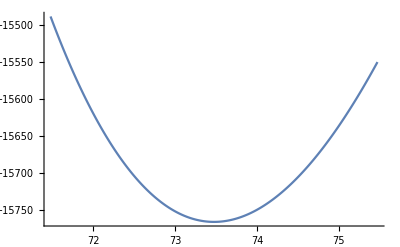

<T>=73.4753

w_0=-0.0394323

W=-0.0000307893

K=-14.9703

Ae^-aT=0.00988648

D_TW=-3.71877×10^-6

```mathematica
Block[{$MaxExtraPrecision=Infinity},
valδw0=0;
vala=2Pi/100;
valb=2Pi/99;
valA=1;
valB=-1.03;


sol=FindMinimum[V*10^(10)/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0},{ReT,62},PrecisionGoal->Infinity,WorkingPrecision->MachinePrecision,MaxIterations->10000,Method->"Newton"];
valT=ReT/.sol[[2]];

range=2*10^(0);

Print[
Plot[V*10^(15)/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0},{ReT,valT-range,valT+range},WorkingPrecision->1000,PlotPoints->200]
];

Print["<T>=",N[valT,3]];
Print["w_0=",-A Abs[a A/(b B)]^(a/(b-a))+B Abs[a A/(b B)]^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}];
Print["W=",N[W/.w0->A (a A/(b B))^(a/(b-a))-B (a A/(b B))^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.T->valT,3]];
Print["K=",N[K/.w0->A (a A/(b B))^(a/(b-a))-B (a A/(b B))^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.{T->valT,T̄->valT},3]];
];

Print["Ae^-aT=",N[A Exp[-a T]/.{A->valA,a->vala,T->valT},3]];
Print["D_TW=",N[DTW/.w0->A (a A/(b B))^(a/(b-a))-B (a A/(b B))^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.{T->valT,T̄->valT},3]];
```

a=(2π)/100, b=(2π)/70

```mathematica
Block[{$MaxExtraPrecision=Infinity},
valδw0=0;
vala=2Pi/100;
valb=2Pi/99;
valA=1;
valB=-1.03;


sol=FindMinimum[V*10^(10)/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0},{ReT,62},PrecisionGoal->Infinity,WorkingPrecision->MachinePrecision,MaxIterations->10000,Method->"Newton"];
valT=ReT/.sol[[2]];

range=2*10^(0);

Print[
Plot[V*10^(15)/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0},{ReT,valT-range,valT+range},WorkingPrecision->1000,PlotPoints->200]
];

Print["<T>=",N[valT,3]];
Print["w_0=",A (a A/(b B))^(a/(b-a))-B (a A/(b B))^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}];
Print["W=",N[W/.w0->A (a A/(b B))^(a/(b-a))-B (a A/(b B))^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.T->valT,3]];
Print["K=",N[K/.w0->A (a A/(b B))^(a/(b-a))-B (a A/(b B))^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.{T->valT,T̄->valT},3]];
];

Print["Ae^-aT=",N[A Exp[-a T]/.{A->valA,a->vala,T->valT},3]];
Print["D_TW=",N[DTW/.w0->A (a A/(b B))^(a/(b-a))-B (a A/(b B))^(b/(b-a))+δw0/.{a->vala,b->valb,A->valA,B->valB,δw0->valδw0}/.{T->valT,T̄->valT},3]];
```

-Graphics-

<T>=73.4753

w_0=-0.000198152

W=-0.0000307893

K=-14.9703

Ae^-aT=0.00988648

D_TW=-3.71877×10^-6